```mathematica
Aatilda = 47 ;
Aptilda =0.05;
(* Aatilda = 48 ;
Aptilda =0.11; *)

deltaa=10^(-0.05 Aatilda)
```

0.00446684

```mathematica
deltap=(10^(0.05Aptilda)-1)/(10^(0.05 Aptilda)+1)
```

0.00287822

```mathematica
delta = Min[deltap,deltaa]
```

0.00287822

```mathematica
Aa= -20Log10[delta]
```

50.8175

```mathematica
Ap=20Log10[(1+delta)/(1- delta)]
```

0.05

```mathematica
alpha = 0.1102(Aa-8.7)
```

4.64135

```mathematica
Dv = (Aa-7.95)/14.36
```

2.9852

```mathematica
Nn=85;
```

```mathematica
Io[x_] := 1+ ∑_(k=1)^Infinity (1/(k!)(x/2)^k)^2
btt[n_]:=alpha √(1-(n/Nn)^2)
```

```mathematica
Wk[n_]:=Io[btt[n]]/Io[alpha]
```

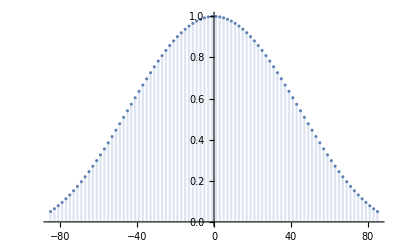

```mathematica
DiscretePlot[Wk[x],{x,-85,85,2},PlotLegends->"Kaiser Window \nα=4.64135\n N=85"]
```

100

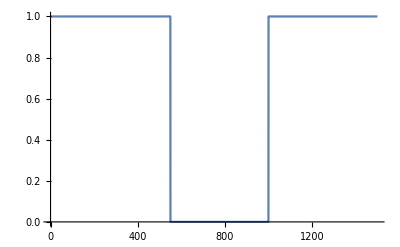

```mathematica
omegap1 = 500;
omegap2 = 1050;
omegaa1 = 600;
omegaa2 = 900;

bt1 = omegaa1-omegap1;
bt2 = omegap2 - omegaa2;
btm=Min[bt1,bt2]
omegaC1= omegap1+bt/2;
omegaC2 = omegap2-bt/2;

h[n_]:=Piecewise[{{1,n<omegaC1},{1,n>omegaC2}}]

Plot[h[n],{n,0,1500},Exclusions->None]
```